# Courses / Andrew Ng Machine Learning / Exercise / 1: Linear Regression

## Introduction

Problem material and description: https://class.coursera.org/ml/assignment

## One-variable linear regression

### Read data

```mathematica
data1=Import[ToFileName[{NotebookDirectory[]},"ex1data1.txt"],"Data"]
```

{{6.1101,17.592},{5.5277,9.1302},{8.5186,13.662},{7.0032,11.854},{5.8598,6.8233},{8.3829,11.886},{7.4764,4.3483},{8.5781,12},{6.4862,6.5987},{5.0546,3.8166},{5.7107,3.2522},{14.164,15.505},{5.734,3.1551},{8.4084,7.2258},{5.6407,0.71618},{5.3794,3.5129},{6.3654,5.3048},{5.1301,0.56077},{6.4296,3.6518},{7.0708,5.3893},{6.1891,3.1386},{20.27,21.767},{5.4901,4.263},{6.3261,5.1875},{5.5649,3.0825},{18.945,22.638},{12.828,13.501},{10.957,7.0467},{13.176,14.692},{22.203,24.147},{5.2524,-1.22},{6.5894,5.9966},{9.2482,12.134},{5.8918,1.8495},{8.2111,6.5426},{7.9334,4.5623},{8.0959,4.1164},{5.6063,3.3928},{12.836,10.117},{6.3534,5.4974},{5.4069,0.55657},{6.8825,3.9115},{11.708,5.3854},{5.7737,2.4406},{7.8247,6.7318},{7.0931,1.0463},{5.0702,5.1337},{5.8014,1.844},{11.7,8.0043},{5.5416,1.0179},{7.5402,6.7504},{5.3077,1.8396},{7.4239,4.2885},{7.6031,4.9981},{6.3328,1.4233},{6.3589,-1.4211},{6.2742,2.4756},{5.6397,4.6042},{9.3102,3.9624},{9.4536,5.4141},{8.8254,5.1694},{5.1793,-0.74279},{21.279,17.929},{14.908,12.054},{18.959,17.054},{7.2182,4.8852},{8.2951,5.7442},{10.236,7.7754},{5.4994,1.0173},{20.341,20.992},{10.136,6.6799},{7.3345,4.0259},{6.0062,1.2784},{7.2259,3.3411},{5.0269,-2.6807},{6.5479,0.29678},{7.5386,3.8845},{5.0365,5.7014},{10.274,6.7526},{5.1077,2.0576},{5.7292,0.47953},{5.1884,0.20421},{6.3557,0.67861},{9.7687,7.5435},{6.5159,5.3436},{8.5172,4.2415},{9.1802,6.7981},{6.002,0.92695},{5.5204,0.152},{5.0594,2.8214},{5.7077,1.8451},{7.6366,4.2959},{5.8707,7.2029},{5.3054,1.9869},{8.2934,0.14454},{13.394,9.0551},{5.4369,0.61705}}

### Use LinearModelFit[]

```mathematica
fittedModel1=LinearModelFit[data1,x,x];
fittedModel1//Normal
```

-3.89578+1.19303 x

```mathematica
Normal[fittedModel1]
```

-3.89578+1.19303 x

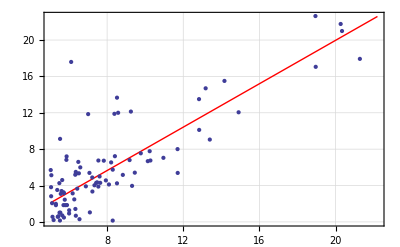

```mathematica
Show[{Plot[fittedModel1[x],{x,Min[data1[[All,1]]],Max[data1[[All,1]]]},Frame-> True,GridLines-> Automatic,GridLinesStyle-> LightGray,PlotStyle-> Red],ListPlot[data1]}]
```

### Use FindFit[] which is more explicit

```mathematica
model[x_]:= Subscript[θ, 0]+Subscript[θ, 1] x;
```

```mathematica
paramters=FindFit[data1,model[x],{Subscript[θ, 0],Subscript[θ, 1]},{x}]
```

{θ_0→-3.89578,θ_1→1.19303}

```mathematica
fittedModel1FindFit[x_]:=model[x]/.paramters
```

```mathematica
Table[{x,fittedModel1FindFit[x]},{x,Min[data1[[All,1]]],Max[data1[[All,1]]]}]
```

{{5.0269,2.10148},{6.0269,3.29451},{7.0269,4.48755},{8.0269,5.68058},{9.0269,6.87361},{10.0269,8.06665},{11.0269,9.25968},{12.0269,10.4527},{13.0269,11.6457},{14.0269,12.8388},{15.0269,14.0318},{16.0269,15.2249},{17.0269,16.4179},{18.0269,17.6109},{19.0269,18.804},{20.0269,19.997},{21.0269,21.19},{22.0269,22.3831}}

```mathematica
Show[{Plot[fittedModel1FindFit[x],{x,Min[data1[[All,1]]],Max[data1[[All,1]]]},Frame-> True,GridLines-> Automatic,GridLinesStyle-> LightGray,PlotStyle-> Red],ListPlot[data1]}]
```

-Graphics-

## Multi-variable linear regression

```mathematica
data2=Import[ToFileName[{NotebookDirectory[]},"ex1data2.txt"],"Data"]
```

{{2104,3,399900},{1600,3,329900},{2400,3,369000},{1416,2,232000},{3000,4,539900},{1985,4,299900},{1534,3,314900},{1427,3,198999},{1380,3,212000},{1494,3,242500},{1940,4,239999},{2000,3,347000},{1890,3,329999},{4478,5,699900},{1268,3,259900},{2300,4,449900},{1320,2,299900},{1236,3,199900},{2609,4,499998},{3031,4,599000},{1767,3,252900},{1888,2,255000},{1604,3,242900},{1962,4,259900},{3890,3,573900},{1100,3,249900},{1458,3,464500},{2526,3,469000},{2200,3,475000},{2637,3,299900},{1839,2,349900},{1000,1,169900},{2040,4,314900},{3137,3,579900},{1811,4,285900},{1437,3,249900},{1239,3,229900},{2132,4,345000},{4215,4,549000},{2162,4,287000},{1664,2,368500},{2238,3,329900},{2567,4,314000},{1200,3,299000},{852,2,179900},{1852,4,299900},{1203,3,239500}}

### Use LinearModelFit[]

```mathematica
fittedModel2[x1_,x2_]:=LinearModelFit[data2,{1,x1,x2},{x1,x2}]
```

```mathematica
Normal[fittedModel2[x1,x2]]
```

89597.9+139.211 x1-8738.02 x2

```mathematica
fittedModel2[1650,3]
```

293081.

```mathematica
plot1=Plot3D[fittedModel2[x1,x2],{x1,Min[data2[[All,1]]],Max[data2[[All,1]]]},{x2,Min[data2[[All,2]]],Max[data2[[All,2]]]},PlotStyle-> Opacity[0.6]]
```

-Graphics3D-

```mathematica
plot2=ListPointPlot3D[data2,PlotStyle->{Red,PointSize[0.1]}]
```

-Graphics3D-

```mathematica
Show[{plot1,plot2}]
```

-Graphics3D-

### Using FindFit[] which is more explicit

```mathematica
model[x1_,x2_]:= Subscript[θ, 0]+Subscript[θ, 1] x1+Subscript[θ, 2] x2;
```

```mathematica
paramters=FindFit[data2,model[x1,x2],{Subscript[θ, 0],Subscript[θ, 1],Subscript[θ, 2]},{x1,x2}]
```

{θ_0→89597.9,θ_1→139.211,θ_2→-8738.02}

```mathematica
paramters=FindFit[data2,model[x1,x2],{Subscript[θ, 0],Subscript[θ, 1],Subscript[θ, 2]},{x1,x2}]
```

{θ_0→89597.9,θ_1→139.211,θ_2→-8738.02}

```mathematica
model2FindFit[x1_,x2_]:=model[x1,x2]/.paramters
```

```mathematica
model2FindFit[1650,3]
```

293081.

```mathematica
Show[{plot2,Plot3D[model2FindFit[x1,x2],{x1,Min[data2[[All,1]]],Max[data2[[All,1]]]},{x2,Min[data2[[All,2]]],Max[data2[[All,2]]]}]}]
```

-Graphics3D-

### Shift and normalize features before fitting

```mathematica
data2Normalized=Transpose[N[(#-Mean[#])/StandardDeviation[#]]&/@Transpose[data2]]
```

{{0.13001,-0.223675,0.475747},{-0.50419,-0.223675,-0.0840744},{0.502476,-0.223675,0.228626},{-0.735723,-1.53777,-0.867025},{1.25748,1.09042,1.59539},{-0.0197317,1.09042,-0.323998},{-0.58724,-0.223675,-0.204036},{-0.721881,-0.223675,-1.13095},{-0.781023,-0.223675,-1.02697},{-0.637573,-0.223675,-0.783051},{-0.0763567,1.09042,-0.803053},{-0.000856737,-0.223675,0.0526819},{-0.139273,-0.223675,-0.0832827},{3.11729,2.40451,2.87498},{-0.921956,-0.223675,-0.643896},{0.376643,1.09042,0.875619},{-0.856523,-1.53777,-0.323998},{-0.962223,-0.223675,-1.12374},{0.765468,1.09042,1.27628},{1.29648,1.09042,2.06804},{-0.294048,-0.223675,-0.699878},{-0.14179,-1.53777,-0.683083},{-0.499157,-0.223675,-0.779852},{-0.0486734,1.09042,-0.643896},{2.37739,-0.223675,1.8673},{-1.13336,-0.223675,-0.72387},{-0.682873,-0.223675,0.992382},{0.661026,-0.223675,1.02837},{0.25081,-0.223675,1.07636},{0.800701,-0.223675,-0.323998},{-0.203448,-1.53777,0.0758745},{-1.25919,-2.85186,-1.36367},{0.0494766,1.09042,-0.204036},{1.42987,-0.223675,1.91529},{-0.238682,1.09042,-0.435962},{-0.709298,-0.223675,-0.72387},{-0.958448,-0.223675,-0.883819},{0.165243,1.09042,0.036687},{2.78635,1.09042,1.66817},{0.202993,1.09042,-0.427165},{-0.423657,-1.53777,0.224627},{0.298626,-0.223675,-0.0840744},{0.712618,1.09042,-0.211234},{-1.00752,-0.223675,-0.331196},{-1.44542,-1.53777,-1.28369},{-0.18709,1.09042,-0.323998},{-1.00375,-0.223675,-0.807044}}

```mathematica
fittedModel2Normalized=LinearModelFit[data2Normalized,{1,x1,x2},{x1,x2}]
```

FittedModel[8.09713×10^-18+0.884766 x1-0.0531788 x2]

```mathematica
normalizeFeature[f_,features_]:=(f-Mean[features])/StandardDeviation[features];
denormalizeFeature[fNoralized_,features_]:=fNoralized*StandardDeviation[features]+Mean[features];
```

```mathematica
fittedModel2Normalized[normalizeFeature[1650,data2[[All,1]]],normalizeFeature[3,data2[[All,2]]]]
denormalizeFeature[%,data2[[All,3]]]
```

-0.378529

293081.

## Mathematica functions

```mathematica
?LinearModelFit
```

LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….
LinearModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,f_2,…},{x_1,x_2,…}] constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… where the f_i depend on the variables x_k. 
LinearModelFit[{m,v}] constructs a linear model from the design matrix m and response vector v.